```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/santanu/Documents/disordered_triangular_swt/calc

```mathematica
RGB[r_,g_,b_]:=RGBColor[r/255.,g/255.,b/255.]
```

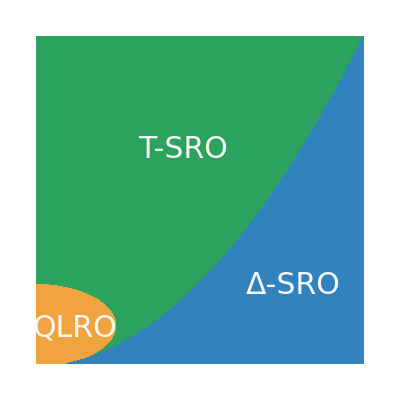
-Graphics-Δ/SubscriptBox[Δ, 0]T/SubscriptBox[T, 0]

```mathematica
KTPHASE = Labeled[RegionPlot[{1/2( 1/T-Δ^2/T^2)≤ 2,1/2(1/T-Δ^2/T^2)>2,T<Δ^2},
{Δ,0.01,1},{T,0.01,1},
PlotStyle->{RGB[44,162,95],
RGB[241,163,64],
RGB[49,130,189]},
BoundaryStyle->None,
Frame->False,
Epilog->{Text[Style["QLRO",RGB[247,247,247],
FontFamily-> "Latin Modern Roman",30],Scaled[{0.13,0.125}]],
Text[Style["T-SRO",RGB[247,247,247],
FontFamily-> "Latin Modern Roman",30],Scaled[{0.45,0.65}]],
Text[Style["Δ-SRO",RGB[247,247,247],
FontFamily-> "Latin Modern Roman",30],Scaled[{0.775,0.25}]]
}],
{Style["Δ/SubscriptBox[Δ, 0]",Black,FontFamily-> "Latin Modern Roman",30],
Style["T/SubscriptBox[T, 0]",Black,FontFamily->"Latin Modern Roman",30]},{Bottom,Left}]
```

```mathematica
Export["bondrandom_kt.pdf",KTPHASE]
```

bondrandom_kt.pdf

```mathematica
TD[Δ0_?NumericQ,T0_?NumericQ]:=First[{T,g}/.NDSolve[{T'[l]==g[l]^2,g'[l]==(2-1/2(1/T[l]-Δ0^2/T[l]^2))g[l],
T[0.0]==T0,g[0.0]==1.0},{T,g},{l,0.0,1.0}]][[1]][1.0]
```

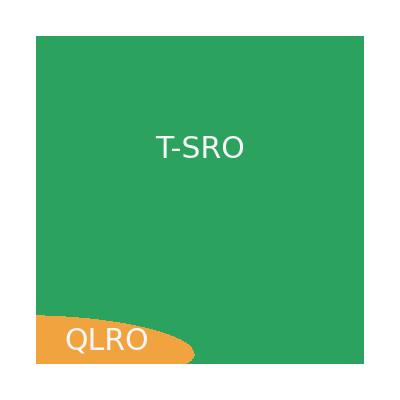
-Graphics-(Δ̃)/Δ_0(T̃)/(SubscriptBox[T, 0]/4)

```mathematica
KTPHASERENORMALIZED = Labeled[RegionPlot[{1/2 (1/TD[x,y]-x^2/TD[x,y]^2)≤ 2,1/2(1/TD[x,y]-x^2/TD[x,y]^2)>2,TD[x,y]<x^2},{x,0.01,0.25},{y,0.01,0.25},
PlotStyle->{RGB[44,162,95],
RGB[241,163,64],
RGB[49,130,189]},
BoundaryStyle->None,
Frame->False,
Epilog->{Text[Style["QLRO",RGB[247,247,247],
FontFamily-> "Latin Modern Roman",30],Scaled[{0.225,0.085}]],
Text[Style["T-SRO",RGB[247,247,247],
FontFamily-> "Latin Modern Roman",30],Scaled[{0.5,0.65}]]}],
{Style["(Δ̃)/Δ_0",Black,FontFamily-> "Latin Modern Roman",30],
Style["(T̃)/(SubscriptBox[T, 0]/4)",Black,FontFamily->"Latin Modern Roman",30]},{Bottom,Left}]
```

```mathematica
Export["bondrandom_kt_renormalized.pdf",KTPHASERENORMALIZED]
```

bondrandom_kt_renormalized.pdf